# Question 01

```mathematica
Exit[]
```

```mathematica
r=ⅇ^Cos[t]-2*Cos[4*t]+Sin[t/12]^5
```

ⅇ^Cos[t]-2 Cos[4 t]+Sin[t/12]^5

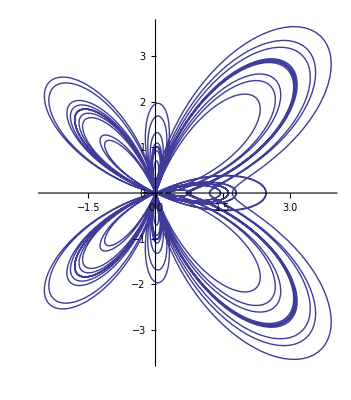

```mathematica
PolarPlot[r,{t,0,24*Pi}]
```

```mathematica
ParametricPlot[r*{Cos[t],Sin[t]},{t,0,24*Pi}]
```

-Graphics-

```mathematica
Exit[]
```

```mathematica
f[x_,y_]:=(x^2*y)/(x^4+4*y^2)
Plot3D[f[x,y],{x,0,10},{y,0,10},Axes->{True,True,False},Boxed->False,AxesLabel->{u,v,w},PlotStyle->{Orange},ColorFunction->"Rainbow",PlotPoints->10]
```

-Graphics3D-

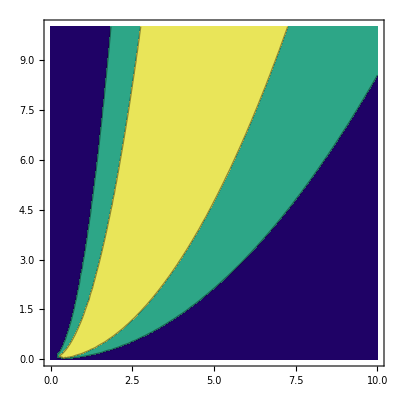

```mathematica
ContourPlot[f[x,y],{x,0,10},{y,0,10},ColorFunction->"BlueGreenYellow",Contours->2,PlotSt]
```

# Question 03

```mathematica
Exit[]
```

```mathematica
n={3,1,5}; r={x,y,z}; r0={-2,1,3};
eq=Solve[n.(r-r0)==0,z][[1,1,2]]
```

1/5 (10-3 x-y)

```mathematica
Plot3D[eq,{x,-5,5},{y,-10,10}]
```

-Graphics3D-

# Question 04

```mathematica
Exit[]
```

```mathematica
eq=x^2/16+y^2/4+z^2==1
```

x^2/16+y^2/4+z^2==1

```mathematica
ParametricPlot3D[{4*Cos[t]*Cos[r],2*Cos[t]*Sin[r],Sin[t]},{t,-π/2,π/2},{r,-π,π},Mesh->None]
ContourPlot3D[x^2/16+y^2/4+z^2==1,{x,-4,4},{y,-2,2},{z,-1,1},BoxRatios->{4,2,1},Mesh->None]
```

-Graphics3D-

-Graphics3D-

# Question 05

```mathematica
Exit[]
```

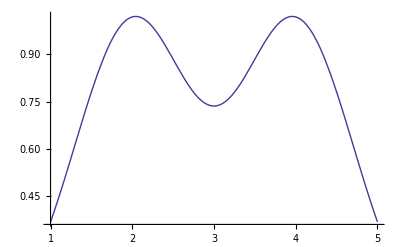

8.76132

-Graphics3D-

-Graphics3D-

61.5638

-Graphics3D-

-Graphics3D-

```mathematica
f[x_]:=ⅇ^(-(x-2)^2)+ⅇ^(-(x-4)^2)
Plot[f[x],{x,1,5}]
∫_1^5 π*f[x]^2 ⅆx//N
RevolutionPlot3D[f[x],{x,1,5},RevolutionAxis->{1,0,0}]
ParametricPlot3D[{f[x]*Cos[t],f[x]*Sin[t],x},{x,1,5},{t,0,2*Pi}]
∫_1^5 2*π*f[x]*xⅆx//N
RevolutionPlot3D[f[x],{x,1,5},RevolutionAxis->{0,0,1}]
ParametricPlot3D[{x*Cos[t],x*Sin[t],f[x]},{x,1,5},{t,0,2*π},BoxRatios->{1,1,.5}]
```

# Question 06

```mathematica
z1=4*x^2+4*y^2; z2=16-4*x^2-4*y^2;
∫_-1^1 ∫_-1^1 (z2-z1)ⅆxⅆy
```

128/3

# Question 07

```mathematica
Exit[]
```

```mathematica
f[x_,y_]:=4-x^2-y^2
ContourPlot3D[z==f[x,y],{x,-2,2},{y,-2,2},{z,0,4},Boxed->False,AxesOrigin->{0,0,0},Mesh->None]
eq=TransformedField["Cartesian"->"Polar",f[x,y],{x,y}->{r,t}];
v=∫_0^(2*Pi) ∫_0^2 eq*rⅆrⅆt;
Print["The volume using this is: ",v]
```

-Graphics3D-

The volume using this is: 8 π

# Question 08

```mathematica
z1=1+x+y; z2=1-x-y;ρ=1+x^2+y^2;
mass=Integrate[Abs[z1-z2]*ρ,{x,0,1},{y,0,1-x}]
```

14/15

# Question 09

```mathematica
Exit[]
```

```mathematica
f[x_,y_]:=4/(x^2+y^2+1)
```

```mathematica
x0=1/2;y0=1;z0=f[x0,y0];r0={x0,y0,z0};r={x,y,z};
n1=D[f[x,y],x]/.{x->x0,y->y0,z->z0};
n2=D[f[x,y],y]/.{x->x0,y->y0,z->z0};
n3=-1;
n={n1,n2,n3};
```

```mathematica
tangent=Solve[(r-r0).n==0,z][[1,1,2]]
```

-16/81 (-19+4 x+8 y)

```mathematica
normal=Solve[(r-r0)==n*t,{x,y,z}]
```

{{x→1/162 (81-128 t),y→1/81 (81-128 t),z→1/9 (16-9 t)}}

```mathematica
table=Table[normal[[1,i,2]],{i,1,3}]
```

{1/162 (81-128 t),1/81 (81-128 t),1/9 (16-9 t)}

```mathematica
g1=Plot3D[f[x,y],{x,-2,2},{y,-2,2}];
g4=Plot3D[tangent,{x,-2,2},{y,-2,2}];
g2=ParametricPlot3D[table,{t,-2,2},PlotStyle->Thickness[.2]];
g3=Graphics3D[{PointSize[.4],Red,Point[r0]}];
Show[g1,g2,g3,g4]
```

-Graphics3D-

11

```mathematica
LessPrime[n_]:=Module[{} , For[i=2,Prime[i]<n,i++,Print[Prime[i]]]]
LessPrime[500]
```

3

5

7

11

13

17

19

23

29

31

37

41

43

47

53

59

61

67

71

73

79

83

89

97

101

103

107

109

113

127

131

137

139

149

151

157

163

167

173

179

181

191

193

197

199

211

223

227

229

233

239

241

251

257

263

269

271

277

281

283

293

307

311

313

317

331

337

347

349

353

359

367

373

379

383

389

397

401

409

419

421

431

433

439

443

449

457

461

463

467

479

487

491

499